Computations on case  2
Two-period design with non-concurrent controls

Set (and simplify) conditions

Note that here we assume r1+r2=1, then r3=0

```mathematica
subst = { r01 -> r1-r11 , r02 -> (1 - r1) - r12 - r22 }
```

{r01→r1-r11,r02→1-r1-r12-r22}

```mathematica
ex={r1->0.4}
```

{r1→0.4}

Define terms to optimise
Note: sigma*term1^(-1)/N is the variance of the estimator of effect 1 (analogously sigma*term2^(-1)/N for effect 2). But since sigma and N are fixed, we simply work on term1 and term2 expressions.

```mathematica
term1=FullSimplify[(r11*r01/(r11+r01))+(r12*r02/(r12+r02))/.subst]
```

r11-r11^2/r1+r12+r12^2/(-1+r1+r22)

```mathematica
term2=FullSimplify[(1/r22 + 1/r02-((1/r02)^2/(1/r01+1/r02+1/r11+1/r12)))^(-1)/.subst]
```

-((-r1^2 (r11+r12)+r1 (r11+r12) (1+r11-r12-r22)+r11^2 (-1+r22)) r22)/(r11^2+r1^2 (r11+r12)-r1 (1+r11-r12) (r11+r12))

```mathematica
sol = Solve[term1 == term2, r12][[1]]
```

{r12→(r1-r1^2-√r1 √(r1-2 r1^2+r1^3+4 r1 r11-4 r1^2 r11-4 r11^2+4 r1 r11^2-4 r1 r22+4 r1^2 r22+4 r1 r22^2))/(2 r1)}

```mathematica
term3=FullSimplify[term1/.sol]
```

(r22 (r1^2-2 r11^2+r1 (-1+2 r11+2 r22)-√r1 √((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2)))/(2 r1 (-1+r1+r22))

```mathematica
e1 = FullSimplify[D[term3, r22]]
```

1/(2 r1 (-1+r1+r22)^2)(r22 (-1+r1+r22) (2 r1-(2 r1^(3/2) (-1+r1+2 r22))/(√((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2)))-r22 (r1^2-2 r11^2+r1 (-1+2 r11+2 r22)-√r1 √((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2))+(-1+r1+r22) (r1^2-2 r11^2+r1 (-1+2 r11+2 r22)-√r1 √((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2)))

```mathematica
e2  =  FullSimplify[D[term3, r11]]
```

(r22 (r1-2 r11+((-1+r1) √r1 (r1-2 r11))/(√((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2))))/(r1 (-1+r1+r22))

```mathematica
sol2=Solve[{r22 (-1+r1+r22) (2 r1-(2 r1^(3/2) (-1+r1+2 r22))/(√((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2)))-r22 (r1^2-2 r11^2+r1 (-1+2 r11+2 r22)-√r1 √((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2))+(-1+r1+r22) (r1^2-2 r11^2+r1 (-1+2 r11+2 r22)-√r1 √((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2))==0,r22 (r1-2 r11+((-1+r1) √r1 (r1-2 r11))/(√((-1+r1) ((-1+r1) r1-4 r1 r11+4 r11^2)+4 (-1+r1) r1 r22+4 r1 r22^2)))   ==0}, {r11,r22}];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

The solutions are then the following

```mathematica
sol2[[11]]
```

{r11→r1/2,r22→1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))))}

```mathematica
sol[[1]]/.sol2[[11]][[2]]
```

r12→1/(2 r1)(r1-r1^2-√r1 √(r1-2 r1^2+r1^3-4 r1 (1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)))))+4 r1^2 (1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)))))+4 r1 ((1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))))))^2+4 r1 r11-4 r1^2 r11-4 r11^2+4 r1 r11^2))

```mathematica
1-r1-sol2[[11]][[2]][[2]]-sol[[1]][[2]]/.sol2[[11]][[2]]
```

-1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))))-1/(2 r1)(r1-r1^2-√r1 √(r1-2 r1^2+r1^3-4 r1 (1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)))))+4 r1^2 (1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)))))+4 r1 ((1-r1+1/2 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/2 √(8 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)-(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))-(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))-1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3)+(-64 (-1+r1)^3+4 (-1+r1) (22-43 r1+21 r1^2)-6 (-4+11 r1-10 r1^2+3 r1^3))/(4 √(4 (-1+r1)^2+1/4 (-22+43 r1-21 r1^2)+(-22+65 r1-64 r1^2+21 r1^3)/(12 (-1+r1))+(2^(1/3) (4-40 r1+129 r1^2-196 r1^3+154 r1^4-60 r1^5+9 r1^6))/(3 (-1+r1) (1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))+1/(48 2^(1/3) (-1+r1))(1024-1536 r1-26112 r1^2+135040 r1^3-304896 r1^4+391296 r1^5-303104 r1^6+139392 r1^7-34560 r1^8+3456 r1^9+√(28311552 r1-467140608 r1^2+3588489216 r1^3-16978083840 r1^4+55228760064 r1^5-130682585088 r1^6+232168882176 r1^7-315144732672 r1^8+329334128640 r1^9-264790867968 r1^10+162331361280 r1^11-74439917568 r1^12+24680595456 r1^13-5573836800 r1^14+764411904 r1^15-47775744 r1^16))^(1/3))))))^2+4 r1 r11-4 r1^2 r11-4 r11^2+4 r1 r11^2))

Plot solutions in period 2 with respect to r1

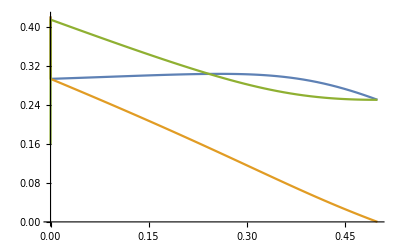

```mathematica
Plot[{sol2[[11]][[2]][[2]],sol[[1]][[2]]/.sol2[[11]][[2]]/.r11->r1/2,1-r1-sol2[[11]][[2]][[2]]-sol[[1]][[2]]/.sol2[[11]][[2]]/.r11->r1/2},{r1,0,.5}]
```

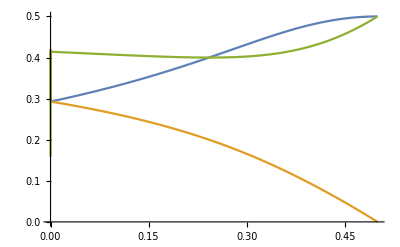

```mathematica
Plot[{sol2[[11]][[2]][[2]]/(1-r1),(sol[[1]][[2]]/.sol2[[11]][[2]]/.r11->r1/2)/(1-r1),1-sol2[[11]][[2]][[2]]/(1-r1)-(sol[[1]][[2]]/.sol2[[11]][[2]]/.r11->r1/2)/(1-r1)},{r1,0,.5}]
```

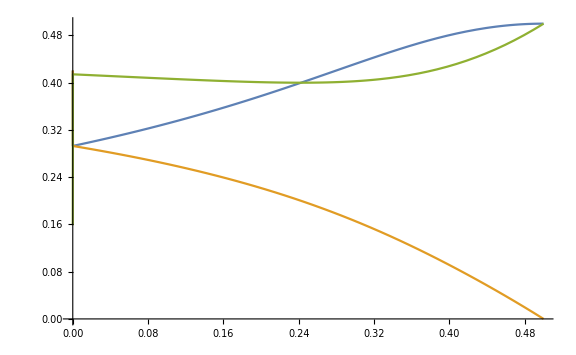

```mathematica
Show[%222,ImageSize->Large]
```

Numerical example:

```mathematica
sol2/.{r1->0.1}
```

{{r22→0.875048-0.110736 ⅈ},{r22→0.875048+0.110736 ⅈ},{r22→0.297642},{r22→1.55226}}

```mathematica
sol/.sol2/.{r1->0.1}
```

{{r12→0.00069231+0.104757 ⅈ},{r12→0.00069231-0.104757 ⅈ},{r12→0.236194},{r12→-0.662421}}

Import solutions to R

```mathematica
CForm[sol2[[11]][[2]][[2]]];
```

```mathematica
CForm[sol[[1]][[2]]]
```

(r1 - Power(r1,2) - Sqrt(r1)*Sqrt(r1 - 2*Power(r1,2) + Power(r1,3) + 4*r1*r11 - 4*Power(r1,2)*r11 - 4*Power(r11,2) + 4*r1*Power(r11,2) - 4*r1*r22 + 4*Power(r1,2)*r22 + 
        4*r1*Power(r22,2)))/(2.*r1)